```mathematica
Remove[aa, dd, BB, CC]
```

```mathematica
aa := 1
dd := 1
rA := 2
```

```mathematica
psi1[x_] := Exp[-k * x] - Exp[k * x]
psi2[x_] := BB * Exp[-k * x] + CC * Exp[k * x]
```

```mathematica
Solve[{
psi1[dd] == psi2[dd],
psi2'[dd] - psi1'[dd] == -aa * psi1[dd]
},{BB, CC}]
```

{{BB→-(-1+ⅇ^(2 k)-2 k)/(2 k),CC→-(ⅇ^(-2 k) (1-ⅇ^(2 k)+2 ⅇ^(2 k) k))/(2 k)}}

```mathematica
BB := -(-1+ⅇ^(2 k)-2 k)/(2 k)
CC := -(ⅇ^(-2 k) (1-ⅇ^(2 k)+2 ⅇ^(2 k) k))/(2 k)
```

```mathematica
eq = FullSimplify[rA * psi2'[rA] / psi2[rA]]
```

(2 k (k+Coth[k] (-1+k Coth[k])))/(-1+2 k Coth[k])

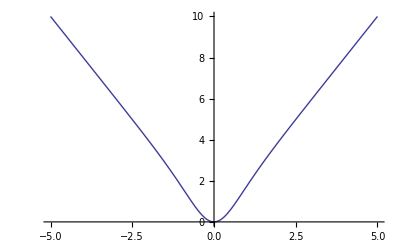

```mathematica
Plot[eq, {k, -5.0, 5.0}]
```

So, we have one state for each value of B > 0